```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Jieyu You\Documents\GitHub\circular-waveguide

```mathematica
Quit[]
```

```mathematica
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[1,2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{0, 0, 0}, {0, 1, 0}, {0, 0, 0}};
λ0=1;k0=2Pi/λ0;
rr=0.3;
sh=Sinh[rr];
ch=Cosh[rr];
r[2]=0λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)γ[i]Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)Cos[k0(r[i]+r[j])];
ΩR =0;
θ=0;
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[1,i,0]+Exp[I θ]Exp[I k0 r[i]]σ[1,i,1],{i,1,1}];

SQ=-0.5sh ch Sum[γp[i,j](Cos[k0 r[α]]Cos[k0 r[3-α]]ρ[t].σ[i,α,β].σ[i,-α+3,β]+Cos[k0 r[α]]Cos[k0 r[3-α]]σ[i,α,β].σ[j,-α+3,β].ρ[t]-2Cos[k0 r[α]]Cos[k0 r[3-α]]σ[j,α,β].ρ[t].σ[i,-α+3,β]),{i,1,atom},{j,1,atom},{α,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,1].σ[j,α,0]+Cos[k0 r[α]]^2σ[i,α,1].σ[j,α,0].ρ[t]-2Cos[k0 r[α]]^2σ[j,α,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{α,1,2}]-0.5 sh^2Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,0].σ[j,α,1]+Cos[k0 r[α]]^2σ[i,α,0].σ[j,α,1].ρ[t]-2 Cos[k0 r[α]]^2σ[j,α,1].ρ[t].σ[i,α,0]),{i,1,atom},{j,1,atom},{α,1,2}]-I Sum[Λ[i,j](Cos[k0 r[α]]Cos[k0 r[α]]σ[i,α,1].σ[j,α,0].ρ[t]-Cos[k0 r[α]]Cos[k0 r[α]]ρ[t].σ[i,α,1].σ[j,α,0]),{i,1,atom},{j,1,atom},{α,1,2}];
DR=-I (V.ρ[t]-ρ[t].V);
solsq=NDSolve[{ρ'[t]==DR+SQ,ρ[0]==init},slnn,{t,0,1000}];
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

```mathematica
Solve[SQ==0,slnn]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a[1,2][t]→0,a[1,3][t]→-(0.252703 γ[1] a[1,1][t])/(-0.807543+1. γ[1]^2),a[2,1][t]→0,a[2,2][t]→(1.72406 (-1.+1. γ[1]^2) a[1,1][t])/(-0.807543+1. γ[1]^2),a[2,3][t]→0,a[3,1][t]→-(1. (0.252703 γ[1]+4.44089×10^-16 γ[1]^3) a[1,1][t])/(-0.807543+1. γ[1]^2),a[3,2][t]→0,a[3,3][t]→(2.97239 (-0.88837+1. γ[1]^2) a[1,1][t])/(-0.807543+1. γ[1]^2)}}

```mathematica
Table[]
```

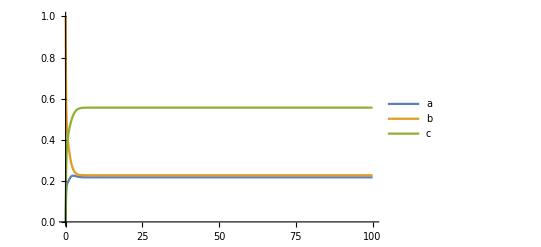

```mathematica
Plot[{a[1,1][t]/.solsq,a[2,2][t]/.solsq,a[3,3][t]/.solsq},{t,0,100},PlotLegends->{"a","b","c"}]
```

```mathematica
ρ[t]/.solsq/.t->100//MatrixForm
```

((0.367098
0.
-0.482013) | (0.
6.70345×10^-7
0.) | (-0.482013
0.
0.632901))

```mathematica
ρ[t]/.solsq/.t->100//MatrixForm
```

((0.216841+0. ⅈ
0.+0.0123819 ⅈ
-0.125486+0. ⅈ) | (0.-0.0123819 ⅈ
0.227011+0. ⅈ
0.+0.0531616 ⅈ) | (-0.125486+0. ⅈ
0.-0.0531616 ⅈ
0.556148+0. ⅈ))

```mathematica
ρ[t]/.solsq/.t->100//MatrixForm
```

((0.197553+0. ⅈ
0.-0.0314797 ⅈ
-0.00516299+0. ⅈ) | (0.+0.0314797 ⅈ
0.294329+0. ⅈ
0.+0.000897745 ⅈ) | (-0.00516299+0. ⅈ
0.-0.000897745 ⅈ
0.508119+0. ⅈ))

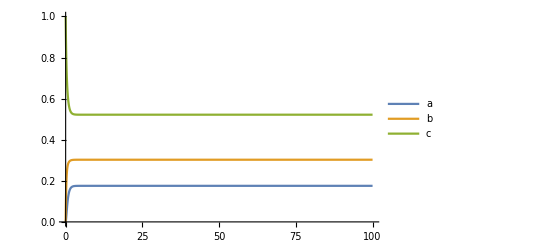

```mathematica
Plot[{a[1,1][t]/.solsq,a[2,2][t]/.solsq,a[3,3][t]/.solsq},{t,0,100},PlotLegends->{"a","b","c"}]
```

```mathematica
(*equal energy gap*)
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[1,2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3;
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
r[5]=1 λ0;
r[4]=0.5λ0;
r[3]=0.5λ0;
r[2]=0 λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)Cos[k0(r[i]+r[j])];
SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α,β].σ[i,αα,β]+σ[i,α,β].σ[j,αα,β].ρ[t]-2σ[j,α,β].ρ[t].σ[i,αα,β]),{i,1,atom},{j,1,atom},{α,1,2},{αα,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,α,1].σ[j,αα,0]+σ[i,α,1].σ[j,αα,0].ρ[t]-2σ[j,αα,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{αα,1,2},{α,1,2}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,αα,0].σ[j,α,1]+σ[i,αα,0].σ[j,α,1].ρ[t]-2σ[j,α,1].ρ[t].σ[i,αα,0]),{i,1,atom},{j,1,atom},{α,1,2},{αα,1,2}]-I Sum[Λ[i,j](σ[i,α,1].σ[j,αα,0].ρ[t]-ρ[t].σ[i,α,1].σ[j,αα,0]),{i,1,atom},{j,1,atom},{α,1,2},{αα,1,2}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000}];
```

```mathematica
ρ[t]/.solsq/.t->1//MatrixForm
```

((0.115262
0.201864
0.197999) | (0.201864
0.442037
0.408364) | (0.197999
0.408364
0.442702))

```mathematica
Out[137]//MatrixForm
```

((0.115262
0.0027956
0.197999) | (0.0027956
0.442037
0.0142419) | (0.197999
0.0142419
0.442702))

```mathematica
sh^2/(1.+2sh^2)
```

0.367099

```mathematica
(*lambda state*)
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[1,2,1]={{0, 0, 1}, {0, 0, 0}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {1, 0, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{0, 0, 0}, {0, 1, 0}, {0, 0, 0}};
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
r[2]=0λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)Cos[k0(r[i]+r[j])];
ΩR =0;
θ=0;
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[1,i,0]+Exp[I θ]Exp[I k0 r[i]]σ[1,i,1],{i,1,1}];

SQ=-0.5sh ch Sum[γp[i,j](Cos[k0 r[α]]Cos[k0 r[3-α]]ρ[t].σ[i,α,β].σ[i,-α+3,β]+Cos[k0 r[α]]Cos[k0 r[3-α]]σ[i,α,β].σ[j,-α+3,β].ρ[t]-2Cos[k0 r[α]]Cos[k0 r[3-α]]σ[j,α,β].ρ[t].σ[i,-α+3,β]),{i,1,atom},{j,1,atom},{α,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,1].σ[j,α,0]+Cos[k0 r[α]]^2σ[i,α,1].σ[j,α,0].ρ[t]-2Cos[k0 r[α]]^2σ[j,α,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{α,1,2}]-0.5 sh^2Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,0].σ[j,α,1]+Cos[k0 r[α]]^2σ[i,α,0].σ[j,α,1].ρ[t]-2 Cos[k0 r[α]]^2σ[j,α,1].ρ[t].σ[i,α,0]),{i,1,atom},{j,1,atom},{α,1,2}]-I Sum[Λ[i,j](Cos[k0 r[α]]Cos[k0 r[α]]σ[i,α,1].σ[j,α,0].ρ[t]-Cos[k0 r[α]]Cos[k0 r[α]]ρ[t].σ[i,α,1].σ[j,α,0]),{i,1,atom},{j,1,atom},{α,1,2}];
DR=-I (V.ρ[t]-ρ[t].V);
solsq=NDSolve[{ρ'[t]==DR+SQ,ρ[0]==init},slnn,{t,0,1000}];
```

```mathematica
ρ[t]/.solsq/.t->50//MatrixForm
```

((0.268524
0.
0.) | (0.
0.268524
0.) | (0.
0.
0.462952))

```mathematica
Quit[]
```

```mathematica
(*V state*)
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};(*2->3*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
σ[1,2,1]={{0, 0, 1}, {0, 0, 0}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {1, 0, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{0, 0, 0}, {0, 1, 0}, {0, 0, 0}};
λ0=1;k0=2Pi/λ0;

sh=Sinh[rr];
ch=Cosh[rr];
r[2]=0λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)Cos[k0(r[i]+r[j])];
ΩR =0;
θ=0;
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[1,i,0]+Exp[I θ]Exp[I k0 r[i]]σ[1,i,1],{i,1,1}];

SQ=-0.5sh ch Sum[γp[i,j](Cos[k0 r[α]]Cos[k0 r[3-α]]ρ[t].σ[i,α,β].σ[i,-α+3,β]+Cos[k0 r[α]]Cos[k0 r[3-α]]σ[i,α,β].σ[j,-α+3,β].ρ[t]-2Cos[k0 r[α]]Cos[k0 r[3-α]]σ[j,α,β].ρ[t].σ[i,-α+3,β]),{i,1,atom},{j,1,atom},{α,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,1].σ[j,α,0]+Cos[k0 r[α]]^2σ[i,α,1].σ[j,α,0].ρ[t]-2Cos[k0 r[α]]^2σ[j,α,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{α,1,2}]-0.5 sh^2Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,0].σ[j,α,1]+Cos[k0 r[α]]^2σ[i,α,0].σ[j,α,1].ρ[t]-2 Cos[k0 r[α]]^2σ[j,α,1].ρ[t].σ[i,α,0]),{i,1,atom},{j,1,atom},{α,1,2}]-I Sum[Λ[i,j](Cos[k0 r[α]]Cos[k0 r[α]]σ[i,α,1].σ[j,α,0].ρ[t]-Cos[k0 r[α]]Cos[k0 r[α]]ρ[t].σ[i,α,1].σ[j,α,0]),{i,1,atom},{j,1,atom},{α,1,2}];
DR=-I (V.ρ[t]-ρ[t].V);
solsq=NDSolve[{ρ'[t]==DR+SQ,ρ[0]==init},slnn,{t,0,1000}];
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

```mathematica
Quit[]
```

```mathematica
atom=1;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;

sh=Sinh[rr];
ch=Cosh[rr];
r[1]=0λ0;
γ[2]=1/ratio;(*lower*)
γ[3]=ratio; (*higher*)
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]+r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;

ω[2]=ω0+δω;
ω[3]=ω0-δω;

SQ=-1/2*sh ch Sum[Exp[I 2(α-1/2)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-1/2(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-1/2 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}];
```

```mathematica
SQ[[1,1]]//Simplify
SQ[[2,2]]//Simplify
SQ[[3,3]]//Simplify
SQ[[1,3]]+SQ[[3,1]]
SQ[[2,3]]
```

-Cosh[rr]^2 a[1,1][t]+Sinh[rr]^2 a[2,2][t]-1/4 Sinh[2 rr] (a[1,3][t]+a[3,1][t])

Cosh[rr]^2 a[1,1][t]+Cosh[rr] Sinh[rr] a[1,3][t]-a[2,2][t]-2 Sinh[rr]^2 a[2,2][t]+Cosh[rr] Sinh[rr] a[3,1][t]+Sinh[rr]^2 a[3,3][t]

Cosh[rr]^2 a[2,2][t]-1/4 Sinh[2 rr] (a[1,3][t]+a[3,1][t])-Sinh[rr]^2 a[3,3][t]

-1/2 Sinh[rr]^2 a[1,3][t]-1/2 (1+Sinh[rr]^2) a[1,3][t]-1/2 Sinh[rr]^2 a[3,1][t]-1/2 (1+Sinh[rr]^2) a[3,1][t]-Cosh[rr] Sinh[rr] (a[1,1][t]-2 a[2,2][t]+a[3,3][t])

-Sinh[rr]^2 a[2,3][t]-1/2 (1+Sinh[rr]^2) (-2 ⅇ^(2 ⅈ t δω) a[1,2][t]+a[2,3][t])-1/2 Cosh[rr] Sinh[rr] (a[2,1][t]-2 ⅇ^(2 ⅈ t δω) a[3,2][t])

```mathematica
SQ[[1,1]]
SQ[[2,2]]
SQ[[3,3]]
```

-(1+Sinh[1]^2) √(γ[1]^2) a[1,1][t]+Sinh[1]^2 √(γ[1]^2) a[2,2][t]-1/2 M ((√γ[1] a[1,3][t])/(√2)+(√γ[1] a[3,1][t])/(√2))

-1/2 (1+Sinh[1]^2) (-2 √(γ[1]^2) a[1,1][t]+a[2,2][t])-1/2 M (-√2 √γ[1] a[1,3][t]-√2 √γ[1] a[3,1][t])-1/2 Sinh[1]^2 (2 √(γ[1]^2) a[2,2][t]-a[3,3][t])

1/2 (1+Sinh[1]^2) a[2,2][t]-1/2 M ((√γ[1] a[1,3][t])/(√2)+(√γ[1] a[3,1][t])/(√2))-1/2 Sinh[1]^2 a[3,3][t]

```mathematica
Solve[{1/4 (-(1+3 Cosh[2 rr]) a[1,2][t]-Sinh[2 rr] a[3,2][t])==0,1/4 (-Sinh[2 rr] a[1,2][t]+(1-3 Cosh[2 rr]) a[3,2][t])==0},{a[1,2][t],a[3,2][t]}]
```

{{a[1,2][t]→0,a[3,2][t]→0}}

```mathematica
(*M and Tr(rho^2)*)
```

```mathematica
Table[atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}];
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{0, 0, 0}, {0, 0, 0}, {0, 0, 1}};
λ0=1;k0=2Pi/λ0;
r[2]=0λ0;
r[1]=-0λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
ratio=0.1;
γ[1]=ratio;
γ[2]=1/ratio;
Λ[i_,j_]:=(*Λ[i,j]=*)1/2Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)√(γ[i]γ[j])Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)√(γ[i]γ[j])Cos[k0(r[i]+r[j])];
SQ=-1/2*m sh ch Sum[γp[i,3-i](ρ[t].σ[i,β].σ[3-i,β]+σ[i,β].σ[3-i,β].ρ[t]-2σ[3-i,β].ρ[t].σ[i,β]),{i,1,2},{β,0,1}]-1/2(sh^2+1)Sum[γ[i,i](ρ[t].σ[i,1].σ[i,0]+σ[i,1].σ[i,0].ρ[t]-2σ[i,0].ρ[t].σ[i,1]),{i,1,2}]-1/2 sh^2Sum[γ[i,i](ρ[t].σ[i,0].σ[i,1]+σ[i,0].σ[i,1].ρ[t]-2σ[i,1].ρ[t].σ[i,0]),{i,1,2}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000}];
{(a[1,1][t]/.solsq/.t->1000)[[1]],(a[2,2][t]/.solsq/.t->1000)[[1]],(a[3,3][t]/.solsq/.t->1000)[[1]]},{m,0.98,1,0.002}]
```

{{0.733209,0.093642,0.173149},{0.751521,0.0867786,0.161701},{0.770953,0.0794953,0.149552},{0.791612,0.0717524,0.136636},{0.813616,0.063505,0.122879},{0.837102,0.0547023,0.108195},{0.862225,0.0452862,0.0924886},{0.889161,0.0351904,0.0756482},{0.918115,0.0243385,0.0575466},{0.94932,0.0126426,0.038037},{0.983052,-5.89993×10^-10,0.0169484}}

```mathematica
Export["pop-inversion2.dat",Out[91]]
```

pop-inversion2.dat

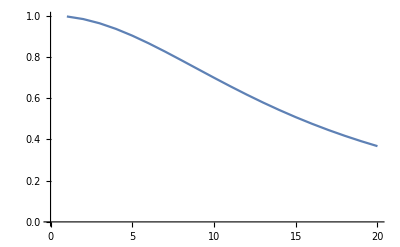

```mathematica
ListLinePlot[Out[118]]
```

```mathematica
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}];
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{0, 0, 0}, {0, 1, 0}, {0, 0, 0}};
λ0=1;k0=2Pi/λ0;
r[2]=0;
r[1]=0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
ratio=0.5;
γ[1]=ratio;
γ[2]=1/ratio;
Λ[i_,j_]:=(*Λ[i,j]=*)1/2Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)√(γ[i]γ[j])Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)√(γ[i]γ[j])Cos[k0(r[i]+r[j])];
δω=0.7;
ω0=100;
ω[1]=ω0+δω;
ω[2]=ω0-δω;
solsq=NDSolve[{ρ'[t]==-1/2* sh ch Sum[γp[i,j]Exp[I 2(β-0.5)(ω[i]+ω[j]-2ω0)t](ρ[t].σ[i,β].σ[j,β]+σ[i,β].σ[j,β].ρ[t]-2σ[j,β].ρ[t].σ[i,β]),{i,1,2},{j,1,2},{β,0,1}]-1/2(sh^2+1)Sum[Exp[I (ω[i]-ω[j])t]γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,2},{j,1,2}]-1/2 sh^2Sum[Exp[-I (ω[i]-ω[j])t]γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,2},{j,1,2}],ρ[0]==init},slnn,{t,0,1000}];
Chop[ρ[t]/.solsq/.t->100,10^-5]//MatrixForm
```

((0.698788
0
-0.458764) | (0
0
0) | (-0.458764
0
0.301203))

```mathematica
Quit[]
```

```mathematica
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}];
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{0, 0, 0}, {0, 1, 0}, {0, 0, 0}};
λ0=1;k0=2Pi/λ0;
r[2]=0;
r[1]=0;
sh=Sinh[rr];
ch=Cosh[rr];
Λ[i_,j_]:=(*Λ[i,j]=*)1/2Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)√(γ[i]γ[j])Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)√(γ[i]γ[j])Cos[k0(r[i]+r[j])];
-1/2* sh ch Sum[γp[i,j](ρ[t].σ[i,β].σ[j,β]+σ[i,β].σ[j,β].ρ[t]-2σ[j,β].ρ[t].σ[i,β]),{i,1,2},{j,1,2},{β,0,1}]-1/2(ch^2)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,2},{j,1,2}]-1/2 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,2},{j,1,2}]//MatrixForm//Simplify;

A=-1/2* sh ch Sum[γp[i,3-i](ρ[t].σ[i,β].σ[3-i,β]+σ[i,β].σ[3-i,β].ρ[t]-2σ[3-i,β].ρ[t].σ[i,β]),{i,1,2},{β,0,1}]-1/2(ch^2)Sum[γ[i,i](ρ[t].σ[i,1].σ[i,0]+σ[i,1].σ[i,0].ρ[t]-2σ[i,0].ρ[t].σ[i,1]),{i,1,2}]-1/2 sh^2Sum[γ[i,i](ρ[t].σ[i,0].σ[i,1]+σ[i,0].σ[i,1].ρ[t]-2σ[i,1].ρ[t].σ[i,0]),{i,1,2}]//Simplify;
A=-1/2*M Sum[γp[i,j]Exp[I 2(β-1/2)(ω[i]+ω[j]-2ω0)t](ρ[t].σ[i,β].σ[j,β]+σ[i,β].σ[j,β].ρ[t]-2σ[j,β].ρ[t].σ[i,β]),{i,1,2},{j,1,2},{β,0,1}]-1/2(sh^2+1)Sum[Exp[I (ω[i]-ω[j])t]γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,2},{j,1,2}]-1/2 sh^2Sum[Exp[-I (ω[i]-ω[j])t]γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,2},{j,1,2}];
```

```mathematica
Collect[A[[2,3]],{a[1,2],a[2,1],a[3,2],a[2,3]}]
```

-1/2 (1+Sinh[rr]^2) (-2 ⅇ^(ⅈ t (-ω[1]+ω[2])) √(γ[1] γ[2]) a[1,2][t]+√(γ[2]^2) a[2,3][t])-1/2 Sinh[rr]^2 (√(γ[1]^2) a[2,3][t]+√(γ[2]^2) a[2,3][t])-1/2 M (ⅇ^(ⅈ t (-2 ω0+ω[1]+ω[2])) √(γ[1] γ[2]) a[2,1][t]-2 ⅇ^(ⅈ t (-2 ω0+2 ω[2])) √(γ[2]^2) a[3,2][t])

```mathematica
Solve[{-ch^2 √(γ[1]^2) a[1,1]+sh^2 √(γ[1]^2) a[2,2][t]-1/2 ch sh √(γ[1] γ[2]) (a[1,3][t]+a[3,1][t])==0,ch^2 √(γ[1]^2) a[1,1][t]+ch sh √(γ[1] γ[2]) a[1,3][t]-sh^2 √(γ[1]^2) a[2,2][t]-ch^2 √(γ[2]^2) a[2,2][t]+ch sh √(γ[1] γ[2]) a[3,1][t]+sh^2 √(γ[2]^2) a[3,3][t]==0,ch^2 √(γ[2]^2) a[2,2][t]-1/2 ch sh √(γ[1] γ[2]) (a[1,3][t]+a[3,1][t])-sh^2 √(γ[2]^2) a[3,3][t]==0,1/2 (-ch sh √(γ[1] γ[2]) a[1,1][t]-(ch^2 √(γ[1]^2)+sh^2 √(γ[2]^2)) a[1,3][t]+ch sh √(γ[1] γ[2]) (2 a[2,2][t]-a[3,3][t]))==0, a[1,1][t]+ a[2,2][t]+a[3,3][t]==0},{a[1,1][t],a[2,2][t],a[3,3][t],a[1,3][t]}]
```

-ch^2 √(γ[1]^2) a[1,1][t]+sh^2 √(γ[1]^2) a[2,2][t]-1/2 ch sh √(γ[1] γ[2]) (a[1,3][t]+a[3,1][t])

```mathematica
Solve[{-ch^2 √(γ[1]^2) a[1,1]+sh^2 √(γ[1]^2) a[2,2] -1/2 ch sh √(γ[1] γ[2]) (a[1,3] +a[3,1] )==0,ch^2 √(γ[1]^2) a[1,1] +ch sh √(γ[1] γ[2]) a[1,3] -sh^2 √(γ[1]^2) a[2,2] -ch^2 √(γ[2]^2) a[2,2] +ch sh √(γ[1] γ[2]) a[3,1] +sh^2 √(γ[2]^2) a[3,3] ==0,ch^2 √(γ[2]^2) a[2,2] -1/2 ch sh √(γ[1] γ[2]) (a[1,3] +a[3,1] )-sh^2 √(γ[2]^2) a[3,3] ==0,1/2 (-ch sh √(γ[1] γ[2]) a[1,1] -(ch^2 √(γ[1]^2)+sh^2 √(γ[2]^2)) a[1,3] +ch sh √(γ[1] γ[2]) (2 a[2,2] -a[3,3] ))==0, a[1,1] + a[2,2] +a[3,3] ==1,a[1,3] ==a[3,1]},{a[1,1] ,a[2,2] ,a[3,3] ,a[1,3] ,a[3,1]}]//Simplify
{{a[1,1]->(sh^6 √(γ[1]^2) γ[2]^2+ch^4 sh^2 γ[1] γ[2] √(γ[2]^2)+ch^2 sh^4 γ[1] (γ[1] √(γ[2]^2)-γ[2] (√(γ[1]^2)+2 √(γ[2]^2))))/(sh^6 √(γ[1]^2) γ[2]^2+ch^6 γ[1]^2 √(γ[2]^2)+ch^4 sh^2 (-3 γ[1] √(γ[1]^2) γ[2]+√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2))+ch^2 sh^4 (√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2)-3 γ[1] γ[2] √(γ[2]^2))),a[2,2]->(ch^2 sh^2 (ch^2 γ[1]-sh^2 γ[2]) (-√(γ[1]^2) γ[2]+γ[1] √(γ[2]^2)))/(sh^6 √(γ[1]^2) γ[2]^2+ch^6 γ[1]^2 √(γ[2]^2)+ch^4 sh^2 (-3 γ[1] √(γ[1]^2) γ[2]+√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2))+ch^2 sh^4 (√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2)-3 γ[1] γ[2] √(γ[2]^2))),a[3,3]->(ch^2 sh^4 γ[1] √(γ[1]^2) γ[2]+ch^6 γ[1]^2 √(γ[2]^2)+ch^4 sh^2 γ[2] (√(γ[1]^2) γ[2]-γ[1] (2 √(γ[1]^2)+√(γ[2]^2))))/(sh^6 √(γ[1]^2) γ[2]^2+ch^6 γ[1]^2 √(γ[2]^2)+ch^4 sh^2 (-3 γ[1] √(γ[1]^2) γ[2]+√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2))+ch^2 sh^4 (√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2)-3 γ[1] γ[2] √(γ[2]^2))),a[1,3]->-((ch sh (ch^2-sh^2)^2 √(γ[1]^2) √(γ[1] γ[2]) √(γ[2]^2))/(sh^6 √(γ[1]^2) γ[2]^2+ch^6 γ[1]^2 √(γ[2]^2)+ch^4 sh^2 (-3 γ[1] √(γ[1]^2) γ[2]+√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2))+ch^2 sh^4 (√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2)-3 γ[1] γ[2] √(γ[2]^2)))),a[3,1]->-((ch sh (ch^2-sh^2)^2 √(γ[1]^2) √(γ[1] γ[2]) √(γ[2]^2))/(sh^6 √(γ[1]^2) γ[2]^2+ch^6 γ[1]^2 √(γ[2]^2)+ch^4 sh^2 (-3 γ[1] √(γ[1]^2) γ[2]+√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2))+ch^2 sh^4 (√(γ[1]^2) γ[2]^2+γ[1]^2 √(γ[2]^2)-3 γ[1] γ[2] √(γ[2]^2))))}}
```